```mathematica
(* Morse oscillator in osc basis , First use diff equation method *)

h=1/√2;V[x_]:=7/(48(.005)) (ⅇ^(-x/7.637626158259733)-1)^2
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-10,10},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.497857}

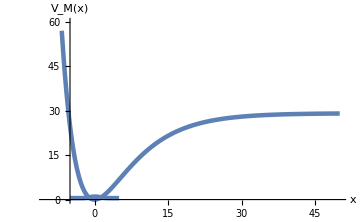

```mathematica
Show[Plot[Evaluate[-h*funs+vals],{x,-5,5},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],Plot[V[x],{x,-10,50},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],PlotRange->{{-10,50},{0,60}},AxesOrigin->{-5,0},ImageSize->Medium]
```

```mathematica
(* Now try Matrix method using osc basis *)

s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{16,16}]
```

SparseArray[…]

```mathematica
Xosc:=N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/2 N[(-s+Transpose[s])]
```

```mathematica
Hmorseosc:= .5Posc.Posc+7/(48(.005))(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + IdentityMatrix[16])
```

```mathematica
Reverse[N[Eigenvalues[Hmorseosc]]]
```

{0.497857,1.48071,2.44648,3.39246,4.31098,5.25424,5.43921,6.40397,7.55802,8.19421,9.30633,10.7216,12.82,20.4905,33.3,56.4453}

```mathematica
Hmorseosc=Chop[Hmorseosc];
SetDirectory[NotebookDirectory[]];
saveHam[ham_] :=Export["./"<>"Hmorseosc.txt", ham, "Table"]

saveHam[Hmorseosc];
```